```mathematica
<<Taggar`MGroups`
```

```mathematica
Subscript[S, 5]=MPermutationsGroup[5]
```

MGroup[…]

```mathematica
raw=MSubgroups[Subscript[S, 5],MPresentation->"Raw"];
```

```mathematica
cvt[{x_,y_}]:={x,"⟨"<>StringTake[ToString@y,{2,-2}]<>"⟩"}
```

```mathematica
subs=raw[[All,1]];
map=Association@Thread[Rule@@@(cvt/@raw)];
```

```mathematica
rules=Select[Tuples[subs,2],SubsetQ[#[[2]],#[[1]]]&];
edges=EdgeList@TransitiveReductionGraph[Rule@@@rules];
```

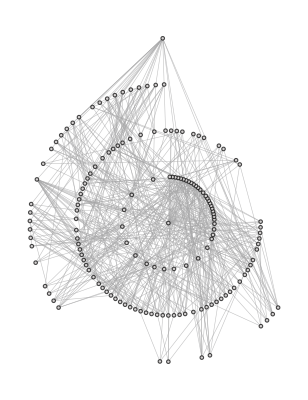

```mathematica
g=Graph[edges,GraphLayout->"RadialEmbedding",VertexSize->1.25,VertexStyle->RGBColor["#D5D2D2"],EdgeShapeFunction->"Line",EdgeStyle->Directive[Thickness[0.001],Lighter[RGBColor["#232326"],0.6]],Background->None]
```

```mathematica
paths=FindPath[g,{Cycles[{{}}]},Sort@MGroupDomain[Subscript[S, 5]],Infinity,All];
```

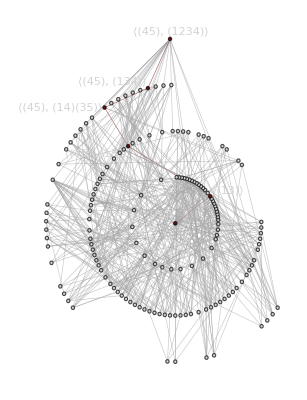

```mathematica
p=paths[[524]];
labels=Thread[p->(map/@p)];
lgh=(Style[#,{RGBColor["#730B0B"],Thick}]&@*Rule)@@@Partition[p,2,1];
pg=PathGraph[p];
hg=HighlightGraph[g,{Style[#,RGBColor["#730B0B"]]&/@p,lgh},VertexLabels->labels,EdgeStyle->RGBColor["#730B0B"],PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"../s5g.svg",hg,Background->None]
```

D:\11\website\resources\mm\../s5g.svg